```mathematica
$Assumptions=And[M>2,df>0,q>0,df<1/2,q<1,M/2∈ℕ];
```

```mathematica
f[β_,M_]=(1-β)/(1-β^M)β^(M/2-1)-1/M;
```

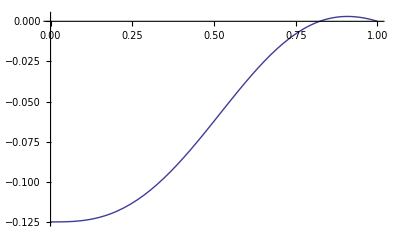

```mathematica
Plot[f[β,8],{β,0,1}]
```

```mathematica
bs[M_]:={sol=FindRoot[f[β,M],{β,0,0.99}];β/.sol}[[1]]
```

```mathematica
bs[4]
```

0.414214

```mathematica
bsplot=Plot[bs[M],{M,2,20},AxesLabel->{M,SuperStar[β]},AxesOrigin->{2,0},PlotStyle->Thick,LabelStyle->Directive[FontSize->20]]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

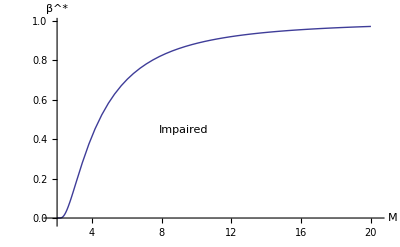

```mathematica
enhlabel=Graphics[Text[Style["Enhanced",20],{6,0.92}]];
```

```mathematica
implabel=Graphics[Text[Style["Impaired",20],{15,0.4}]];
```

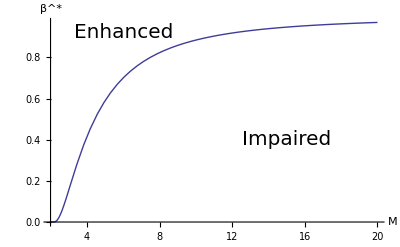

```mathematica
bslabelled=Show[bsplot,enhlabel,implabel]
```

```mathematica
g[df_,β_,M_]=2((1-2df)-β(1+2df))/((1-2df)^M-β^M(1+2df)^M)β^(M/2-1)(1-2df)^(M/2-1)(1+2df)^(M/2-1);
```

```mathematica
dfs[β_,M_]:={sol=FindRoot[g[df,β,M]-g[0,β,M]/2,{df,0,0.5}];df/.sol}[[1]]
```

```mathematica
dfs1[M_]:={sol=FindRoot[g[df,1,M]-1/M,{df,0.0001,0.5}];df/.sol}[[1]]
```

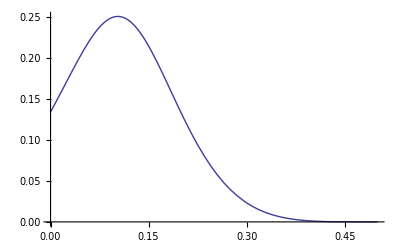

```mathematica
Plot[g[df,2/3,10],{df,0,0.5},PlotRange->Full]
```

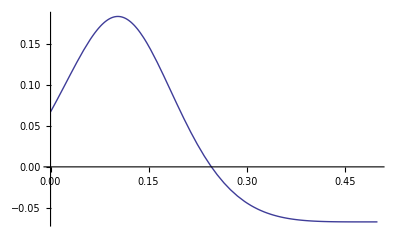

```mathematica
Plot[g[df,2/3,10]-g[0,2/3,10]/2,{df,0,0.5},PlotRange->Full]
```

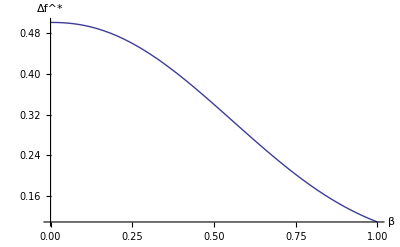

```mathematica
dfsplot=Plot[dfs[β,10],{β,0,1},AxesLabel->{β,SuperStar[Δf]},PlotStyle->Thick,LabelStyle->Directive[FontSize->20]]
```

```mathematica
enhlabel2=Graphics[Text[Style["Enhanced",20],{0.3,0.25}]];
```

```mathematica
implabel2=Graphics[Text[Style["Impaired",20],{0.7,0.4}]];
```

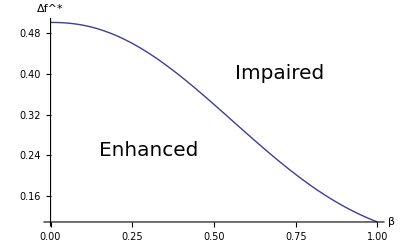

```mathematica
dfslabelled=Show[dfsplot,enhlabel2,implabel2]
```

```mathematica
Export["./GitHub/Complex_Synapse/MHCpaper/Figures/multistate_betastar.eps",bslabelled]
```

./GitHub/Complex_Synapse/MHCpaper/Figures/multistate_betastar.eps

```mathematica
Export["./GitHub/Complex_Synapse/MHCpaper/Figures/multistate_deltafstar.eps",dfslabelled]
```

./GitHub/Complex_Synapse/MHCpaper/Figures/multistate_deltafstar.eps

```mathematica
dfs[2/3,10]
```

-0.246009

```mathematica
dfs1[10]
```

0.109937

```mathematica
dfs[0.75,10]
```

-0.202868

```mathematica
dfs[0.999,10]
```

0.110185